```mathematica
F[x_]=3 x^4-16 x^3+24x; (*задана функція*)
```

```mathematica
A=3.; (*початок відрізку пошуку*) 
B=4.; (*кінець відрізку пошуку*)

ϵ=0.001;      (*точність*)
```

```mathematica
result={};
```

```mathematica
min=Minimize[F[x], A<x<B, x] (*знаходження мінімума функції*)
```

{-161.568,{x→3.8662}}

```mathematica
(*Графік функції*)
```

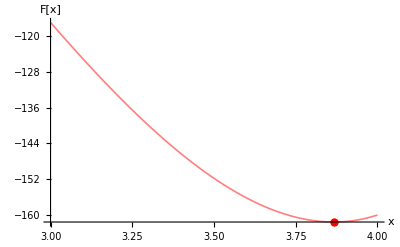

```mathematica
Plot[F[x], {x, A, B}, PlotRange->All, PlotStyle-> {Pink,Thickness[0.003]}, AxesLabel->{x, "F[x]"}, Epilog->{Red, PointSize[0.015], Point[{min[[2,1,2]], min[[1]] }]}]
```

```mathematica
(*метод Фібоначі*)
a0=A;
b0=B;
m={};(*масив чисел Фібоначчі*)
For[i=1, i < 100000, i++, (*розраховуємо числа фібоначі*)
{s=Fibonacci[i];
AppendTo[m, s];
If[Fibonacci[i] ≥  (b0-a0)/ϵ,  Break[]]
}]
m0=Delete[m, -1];
NN=i; (*кількість
обчислень цільової функції,при реалізації ітераційного процесу для Вольфраму*)
n=NN-1;
(*1 ітерація*)
j=1;
aj=a0;
bj=b0;
abj={};
(*масив кінців відрізка*)
AppendTo[abj, {aj, bj}];
x1j=aj+m[[NN-j-1]]/m[[NN-j+1]]×(bj-aj)-(-1)^(n-j+1)/m[[NN-j+1]]×ϵ;
x2j=aj+m[[NN-j]]/m[[NN-j+1]]×(bj-aj)+(-1)^(n-j+1)/m[[NN-j+1]]×ϵ;
Fx1j=F[x1j];
Fx2j=F[x2j];
Fxj={};(*масив з-ь ф-ції*)
AppendTo[Fxj, {Fx1j, Fx2j}]; 
xj={};(*масив аргументів (x1j, x2j на кожній ітерації)*)
AppendTo[xj, {x1j, x2j}]; 
res3={};
AppendTo[res3,{1,xj[[-1,1]],xj[[-1,2]],Fxj[[-1,1]],Fxj[[-1,2]],Abs[abj[[-1,1]]-abj[[-1,2]]]}];
If[Fxj[[j,1]]≥ Fxj[[j,2]], {aj= xj[[j, 1]];
bj=abj[[j, 2]];
AppendTo[abj, {aj, bj}]; 
x1j = xj[[j, 2]];
 Fx1j = F[xj[[j, 2]]];
x2j =  aj+m[[NN-j-1]]/m[[NN-j]]×(bj-aj)+(-1)^(n-j)/m[[NN-j]]×ϵ;
AppendTo[xj, {x1j, x2j}];
 Fx2j = F[xj[[j+1, 2]]];
AppendTo[Fxj, {Fx1j, Fx2j}]; }, 
{aj=abj[[j, 1]];
bj= xj[[j, 2]];
AppendTo[abj, {aj, bj}];
x2j = xj[[j, 1]];
 Fx2j = F[xj[[j, 1]]];
x1j = aj+m[[NN-j-2]]/m[[NN-j]]×(bj-aj)-(-1)^(n-j)/m[[NN-j]]×ϵ;
AppendTo[xj, {x1j, x2j}];
 Fx1j = F[xj[[j+1, 1]]];
AppendTo[Fxj, {Fx1j, Fx2j}];}]
If[Abs[abj[[-1,2]]-abj[[-1,1]]]≤  ϵ,Break[]];
AppendTo[res3,{2,xj[[-1,1]],xj[[-1,2]],Fxj[[-1,1]],Fxj[[-1,2]],Abs[abj[[-1,1]]-abj[[-1,2]]]}];
(*цикл методу*)
t1j=AbsoluteTime[];
For[j = 2, j < 100000, j++,
{If[Fxj[[j,1]]≥ Fxj[[j,2]], {aj= xj[[j, 1]];
bj=abj[[j, 2]];
AppendTo[abj, {aj, bj}];
x1j = xj[[j, 2]];
 Fx1j = F[xj[[j, 2]]];
x2j =  aj+m[[NN-j-1]]/m[[NN-j]]×(bj-aj)+(-1)^(n-j)/m[[NN-j]]×ϵ;
AppendTo[xj, {x1j, x2j}];
 Fx2j = F[xj[[j+1, 2]]];
AppendTo[Fxj, {Fx1j, Fx2j}]; }, 
{aj=abj[[j, 1]];
bj= xj[[j, 2]];
AppendTo[abj, {aj, bj}]; 
x2j = xj[[j, 1]];
 Fx2j = F[xj[[j, 1]]];
x1j = aj+m[[NN-j-2]]/m[[NN-j]]×(bj-aj)-(-1)^(n-j)/m[[NN-j]]×ϵ;
AppendTo[xj, {x1j, x2j}];
 Fx1j = F[xj[[j+1, 1]]];
AppendTo[Fxj, {Fx1j, Fx2j}];}];
AppendTo[res3,{j+1,xj[[-1,1]],xj[[-1,2]],Fxj[[-1,1]],Fxj[[-1,2]],Abs[abj[[-1,1]]-abj[[-1,2]]]}];
If[Round[Abs[abj[[-1,1]]-abj[[-1,2]]], ϵ]≤  ϵ,Break[]];
If[j > 100, Break[], Continue[]];}] 
t2j=AbsoluteTime[];
Grid[Prepend[res3,{"k","x_1^(k)","x_2^(k)","F[x_1^(k)]"," F[x_2^(k)]","Abs[b-a]"}]]
Print["Час роботи циклу\t",t=t2j-t1j,"\nОтримане наближення\t", xsj=(abj[[-1,1]]+abj[[-1,2]])/2,"\nЗначення функції\t", F[(abj[[-1,1]]+abj[[-1,2]])/2],"\nДовжина інтервалу невизначеності\t",Round[Abs[abj[[-1,1]]-abj[[-1,2]]], 0.001]]
A3=Abs[xsj-c];
AppendTo[result,{n-1,abj[[-1,1]],abj[[-1,2]],Round[Abs[abj[[-1,1]]-abj[[-1,2]]], 0.001],A3, t,n,xsj,F[xsj]}];
```

{Null}

k | x_1^(k) | x_2^(k) | F[x_1^(k)] |  F[x_2^(k)] | Abs[b-a]
1 | 3.38197 | 3.61803 | -145.281 | -156.88 | 1.
2 | 3.61803 | 3.76393 | -156.88 | -160.727 | 0.618034
3 | 3.76393 | 3.8541 | -160.727 | -161.556 | 0.381966
4 | 3.8541 | 3.90983 | -161.556 | -161.407 | 0.236069
5 | 3.81966 | 3.8541 | -161.39 | -161.556 | 0.145897
6 | 3.8541 | 3.87538 | -161.556 | -161.561 | 0.0901722
7 | 3.87538 | 3.88855 | -161.561 | -161.526 | 0.0557245
8 | 3.86727 | 3.87538 | -161.568 | -161.561 | 0.0344477
9 | 3.86221 | 3.86727 | -161.567 | -161.568 | 0.0212768
10 | 3.86727 | 3.87031 | -161.568 | -161.567 | 0.0131709
11 | 3.86525 | 3.86727 | -161.568 | -161.568 | 0.00810582
12 | 3.86423 | 3.86525 | -161.568 | -161.568 | 0.00506512
13 | 3.86525 | 3.86626 | -161.568 | -161.568 | 0.0030407
14 | 3.86626 | 3.86627 | -161.568 | -161.568 | 0.00202442
15 | 3.86526 | 3.86626 | -161.568 | -161.568 | 0.00101628

Час роботи циклу	0.010695
Отримане наближення	3.86576
Значення функції	-161.568
Довжина інтервалу невизначеності	0.001